Тема 9. Обчислення границь та похідних

Завдання 1. Послідовність з раціональним загальним членом.

Використовуючи систему «Mathematica», обчислити границю послідовності та надрукувати вісім початкових членів. Якщо знаменник дробу обертається на 0 при n=1 або n=2 , то починайте генерувати послідовність з більшого значення n, наприклад, n = 3.

```mathematica
Remove[x,n]
```

```mathematica
x[n_]=((1-n)^4-(1+n)^4)/((1+n)^3-(1-n)^3);
Table[x[n],{n,1,8}]
```

{-2,-20/7,-10/3,-68/19,-26/7,-148/39,-50/13,-260/67}

```mathematica
N[Table[x[n],{n,1,8}]]
```

{-2.,-2.85714,-3.33333,-3.57895,-3.71429,-3.79487,-3.84615,-3.8806}

```mathematica
Limit[x[n],n->∞]
```

-4

Завдання 2. Послідовність з ірраціональним загальним членом.

Використовуючи систему «Mathematica», обчислити границю послідовності, надрукувати 8 початкових членів в десятковому вигляді,
побудувати графік перших 50 членів. Вертикальний діапазон графіка підібрати самостійно. Інколи перші члени послідовності сильно відрізняються від
граничного значення. Тоді послідовність можна генерувати, починаючи з 5-го, або більшого за номером члена.

```mathematica
Remove[x,n]
```

```mathematica
x[n_]=((n^2-1)^(1/3)+7*n^3)/((n^12+n+1)^(1/4)-n);
```

```mathematica
N[Table[x[n],{n,1,8}]]
```

{22.1467,9.57137,7.95832,7.50777,7.3157,7.21558,7.15665,7.11901}

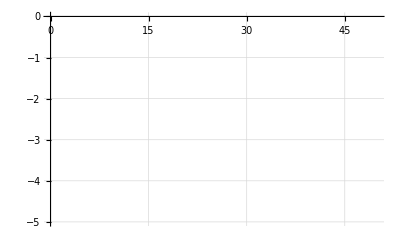

```mathematica
ListPlot[Table[x[n],{n,1,50}],PlotStyle->PointSize[0.02],PlotRange->{-5,0},GridLines->Automatic,Filling->Axis]
```

```mathematica
Limit[x[n],n->∞]
```

7

Завдання 3. Границі різноманітних функцій.

Використовуючи систему «Mathematica», обчислити границю функції. Перевірити, що значення функції наближаються до границі, коли аргумент x прямує до граничного значення x0. Для цього побудувати таблицю значень функції в околі граничного значення x0.

```mathematica
f[x_]=(Tan[x]-Tan[π/3])/(Log[x]-Log[π/3]);
x0=π/3;
y0=Limit[f[x],x->x0];
N[y0]
```

4.18879

```mathematica
f[x0+{0.1,0.01,0.001,0.0001,0.00001,0.000001}]//TableForm
```

5.32601
4.28309
4.19806
4.18972
4.18888
4.1888

Завдання 4. Границя раціональної функції в околі особливої точки.

Використовуючи систему «Mathematica», обчислити границю раціональної функції. Перевірити, що гранична точка є особливою точкою функції. Показати, що значення функції наближаються до граничного, коли аргумент x прямує до граничного значення. Для цього побудувати графік функції в околі особливої точки і зобразити цю точку. Інтервал зміни абсциси в околі особливої точки підібрати самостійно.

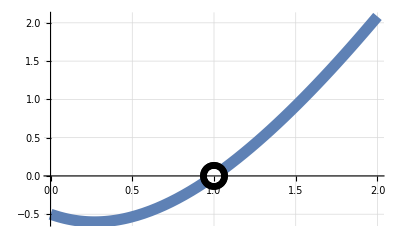

```mathematica
f[x_]=((2*x^2-x-1)^2)/(x^3+2*x^2-x-2);
x0=1;
y0=Limit[f[x],x->x0];
p1=ListPlot[{{x0,y0}},PlotStyle->{Black,PointSize[0.05]}];
p2=ListPlot[{{x0,y0}},PlotStyle->{White,PointSize[0.025]}];
pline=Plot[f[x],{x,x0-1,x0+1},PlotStyle->Thickness[0.02]];
Show[pline,p1,p2,AxesOrigin->{0,0},GridLines->Automatic]
```

Завдання 5. Обчислення похідних.

Використовуючи систему «Mathematica», обчислити похідну y’(x) функції y(x) . Побудувати графік функції y(x) та її похідної y’(x). Обчислити значення похідної в точках x = 0.5,1, 3.0 . При побудові графіків інтервал незалежної змінної підібрати самостійно.

```mathematica
y[x_]=(2*x^2-x-1)/(3 √(2+4*x));
y1[x_]=Simplify[D[y[x],x]]
```

{8,3,-2}[(-1-x+2 x^2)/(3 √(2+4 x)),x]

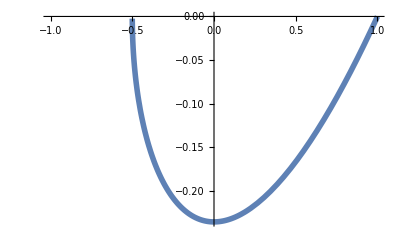

```mathematica
Plot[y[x],{x,1,-1},PlotStyle->Thickness[0.01]]
```

```mathematica
Plot[y1[x],{x,1,-1},PlotStyle->Thickness[0.01]]
```

-Graphics-

```mathematica
y1[{0.5,1,3}]
```

{8,3,-2}[{-0.166667,0,(√14)/3},{0.5,1,3}]

Завдання 6. Похідні виразів, які містять тригонометричні функції.

Використовуючи систему «Mathematica», знайти похідну y’(x) функції y(x) та побудувати її графік. Інтервал абсцис на графіку підібрати самостійно.

```mathematica
y[x_]=Cot[5^(1/3)]-1/8*Cos[4*x]^2/Sin[8*x];
y1[x_]=Simplify[D[y[x],x]]
```

{8,3,-2}[Cot[5^(1/3)]-1/16 Cot[4 x],x]

```mathematica
Plot[y1[x],{x,1,-1},PlotStyle->Thickness[0.01]]
```

-Graphics-

Завдання 7. Похідні вищих порядків.

Використовуючи систему «Mathematica», знайти похідну зазначеного порядку та побудувати її графік. Інтервал незалежної змінної на графіку в кожній задачі підбирати самостійно.

```mathematica
y[x_]=(5*x-1)*Log[x]^2;
```

```mathematica
y3[x_]=Simplify[D[y[x],{x,3}]]
```

{8,3,-2}[(-1+5 x) Log[x]^2,{x,3}]

```mathematica
Plot[y3[x],{x,10,0},PlotStyle->Thickness[0.01]]
```

-Graphics-

Завдання 8. Використання похідних у рівняннях.

Використовуючи систему «Mathematica», показати, що функція y(x) задовольняє рівнянню. В кожному варіанті задана функція та рівняння, якому вона можливо задовольняє.

```mathematica
y[x_]=2+√(1-x^2);
y1[x_]=Simplify[D[y[x],x]]
```

{8,3,-2}[2+√(1-x^2),x]

```mathematica
Simplify[(1-x^2)*y1[x]+x*y[x]==2*x]
```

x √(1-x^2)==(-1+x^2) {8,3,-2}[2+√(1-x^2),x]